```mathematica
E0=2;
```

```mathematica
list={};
For[i=1,i<10,i=i+0.1,
AppendTo[list,Plot[E0*Cos[i*t],{t,-10,10},Epilog->Inset[i,{0.2,0.9}]]];

]
```

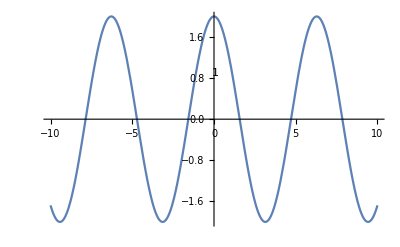
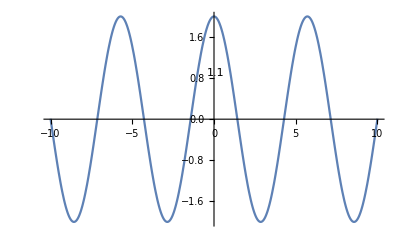
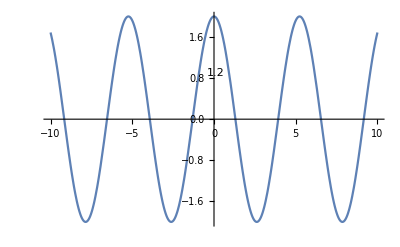
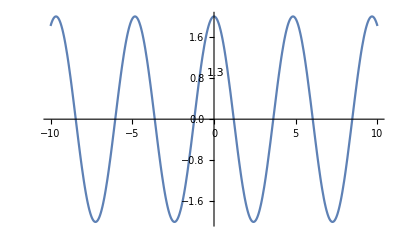
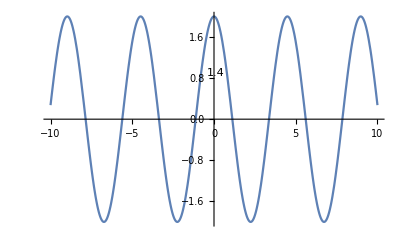
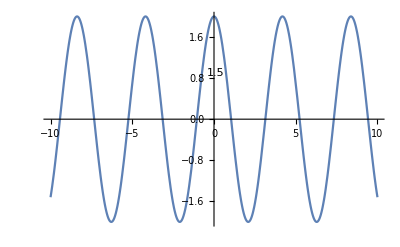
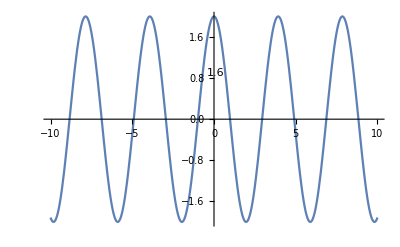
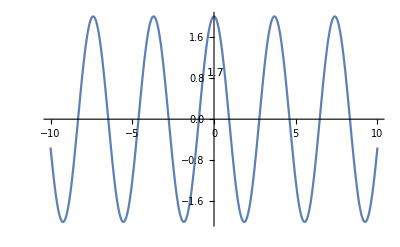

```mathematica
list[[1;;20]]
```

```mathematica
Export["C:\\Users\\zxs20\\Downloads\\testlalala.avi",list,"AVI"];
```

```mathematica
SystemOpen["C:\\Users\\zxs20\\Downloads\\testlalala.avi"]
```